Άσκηση 7.5.3-1

Εφαρμόστε την πορεία των δύο προηγούμενων παραδειγμάτων για να κάνετε μια εκτίμηση του ολοκληρώματος

∫_0^1 √(1-x^2)ⅆx=π/4≃0.785398

Λύση

Επιλέγουμε τη συνάρτηση βάρους ρ(x)=1/2(3-2x), έτσι ώστε να ικανοποιεί τις συνθήκες που θέλουμε.

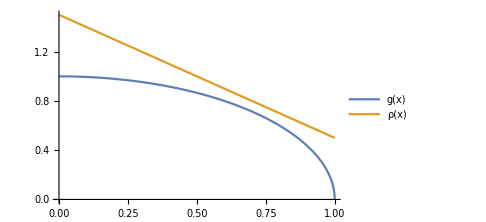
∫_0^1 ρ(x)ⅆx = 1
-Graphics-

```mathematica
ClearAll["Global`*"]
g[x_]:=√(1-x^2);
ρ[x_]:=1/2(3-2x);
Integrate[ρ[x],{x,0,1}];
Column[{
StringForm["∫_0^1 ρ(x)ⅆx = ``",%],
Plot[{g[x],ρ[x]},{x,0,1},ImageSize->Medium,PlotLegends->LineLegend[Automatic,{"g(x)","ρ(x)"}]]
},Alignment->Center]
```

Θα έχουμε λοιπόν

ⅆy=ρ(x)ⅆx | ⇒ | y(x)=3/2(x-x^2) | ⇒ | y(x)=1/2(3-√(9-8y))

Ορίζουμε τώρα την g̃(y)=g(x(y))/ρ(x(y))

Με τη βοήθεια αυτής υπολογίζουμε την τιμή του ολοκληρώματος και την διασπορά του εκτιμητή από την τιμή της συνάρτησης g̃(y) σε N σημεία.

I=1/N∑g̃(y_i)
var(G)=1/N[1/N∑(g̃)^2(y_i)-(1/N∑g̃(y_i))^2]

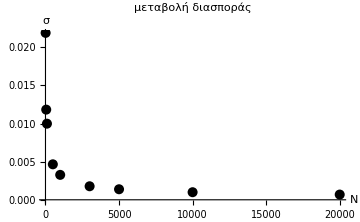
| Ι | σ
10 | 0.832005 | 0.0218956
50 | 0.794558 | 0.0118286
100 | 0.780189 | 0.00998603
500 | 0.778884 | 0.00465503
1000 | 0.780603 | 0.00327034
3000 | 0.785305 | 0.0017751
5000 | 0.786744 | 0.00138295
10000 | 0.785682 | 0.000994173
20000 | 0.787203 | 0.000686369

-Graphics-

```mathematica
gg[y_]:=√((-14+6 √(9-8 y)+8 y)/(9-8 y));ns={10,50,100,500,1000,3000,5000,10000,20000};
res=Reap@Do[
pts=RandomReal[1,{n}];
Sow[G=Mean@Map[gg[#]&,pts],III];
Sow[√(1/n(Mean@Map[gg[#]^2&,pts]-G^2)),σσσ];
,{n,ns}];
Column[{
TableForm[Transpose@res[[2]],TableAlignments->Center,TableHeadings->{ns,{"Ι","σ"}}],"",
ListPlot[Transpose@{ns,res[[2,2]]},ImageSize->Medium,PlotLabel->"μεταβολή διασποράς",PlotStyle->{Black,PointSize[0.02]},PlotRange->All,AxesLabel->{"N","σ"}]
},Alignment->Center]
```

Παρατηρούμε ότι όπως ανεβάζουμε τα σημεία πλησιάζουμε την τιμή του ολοκληρώματος ικανοποιητικά. Φαίνεται όμως ότι ο ρυθμός μείωσης της διασποράς ελαττώνεται όσο αυξάνουμε τα σημεία, επομένως η μέθοδος δίνει αρκετά ακριβές αποτέλεσμα χωρίς να χρειαστεί να υπολογίσουμε τα παραπάνω σε πάρα πολλά σημεία.

Άσκηση 7.5.3-2

Με τη μέθοδο MC να υπολογιστεί η τιμή του ολοκληρώματος

I=∫_0^∞ ⅇ^-x g(x)ⅆx=1

και η τυπική απόκλιση του εκτιμητή, όταν g(x)=x, x^2, x^3. Μπορεί να εξηγηθεί η συμπεριφορά της τυπικής απόκλισης;

Λύση

Κάνουμε την αλλαγή μεταβλητής x(y)=-ln(1-y), y∈[0,1), έτσι ώστε να χρησιμοποιήσουμε την ομοιόμορφη κατανομή για την επιλογή των τυχαίων τιμών του ολοκληρώματος. Επομένως το ολοκλήρωμα γράφεται:

I=∫_0^1 ⅇ^(ln(1-y))/(1-y)g(x(y))ⅆy

```mathematica
ClearAll["Global`*"]
g[y_,i_]:={-Log[1-y],Log[1-y]^2,-Log[1-y]^3}[[i]];
f[y_,i_]:=ⅇ^Log[1-y]/(1-y)g[y,i];
n=50000;pts=RandomReal[1,{n}];
at=Integrate[{ⅇ^-x x,ⅇ^-x x^2,ⅇ^-x x^3},{x,0,∞}];
res=Table[{at[[i]],
G=Mean@Map[f[#,i]&,pts],
√(1/n(Mean@Map[f[#,i]^2&,pts]-G^2))
},{i,1,3}];
TableForm[res,TableAlignments->Center,TableHeadings->{{"g(x)=x","g(x)=x^2","g(x)=x^3"},{"αναλ. τιμή","Ι","σ"}}]
```

| αναλ. τιμή | Ι | σ
g(x)=x | 1 | 1.00181 | 0.00448781
g(x)=x^2 | 2 | 2.01065 | 0.0198706
g(x)=x^3 | 6 | 6.02809 | 0.109784

Παρατηρούμε ότι η τιμή του ολοκληρώματος που υπολογίζουμε (για N=50000 σημεία) είναι κοντά στην αναλυτική τιμή κάθε φορά. Παρόλ’ αυτά, η διασπορά αυξάνεται ραγδαία. Αυτό οφείλεται στην συμπεριφορά της ολοκληρωτέας συνάρτησης στο διάστημα που μας ενδιαφέρει. Όπως φαίνεται αν τις σχεδιάσουμε, αυτή που αφορά την g(x)=x^3 αυξάνει πολύ πιο απότομα από τις άλλες δύο όσο πλησιάζουμε στο 1.

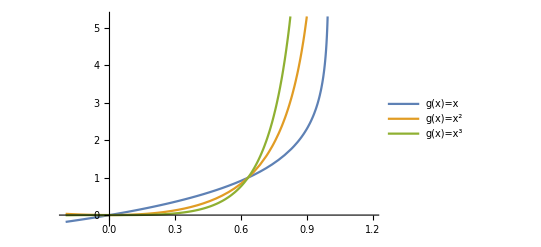

```mathematica
Plot[Evaluate@Table[f[y,i],{i,1,3}],{y,-0.2,1.2},PlotLegends->LineLegend[Automatic,{"g(x)=x","g(x)=x^2","g(x)=x^3"}]]
```

Άσκηση 7.5.4-1

Να υπολογιστεί το ολοκλήρωμα

I=∫_0^2 1/(1+x^2)ⅆx=1.10715

χρησιμοποιώντας τη συνάρτηση βάρους ρ(x)=1-0.5x και την αριθμητική μέθοδο εύρεσης TA.

Λύση

Η αριθμητική μέθοδος εύρεσης τυχαίων αριθμών βασίζεται στην αναδρομική σχέση:

x_(j+1)=x_j+1/(N ρ(x_j)),

η οποία ξεκινάει από την τιμή x_0=0 και μας δίνει N ψευδοτυχαίους αριθμούς.

Υπολογίζουμε επίσης την g̃(y) για την μέθοδο MC.

g̃(y)=1/([1-(1-√(1-y))][1+4(1-√(1-y))]), y∈[0,1]

Επίσης κάνουμε τον υπολογισμό χρησιμοποιώντας μια γεννήτρια ψευδοτυχαίων αριθμών (εσωτερική συνάρτηση στη Mathematica).

```mathematica
ClearAll["Global`*"]
n=50000;
x[0]=0;
g[x_]:=1/(1+x^2);
ρ[x_]:=1-0.5x;
gg[y_]:=1/((1-(1-√(1-y))) (1+4 (1-√(1-y))^2));
x[j_]:=x[j]=x[j-1]+1+1/(n ρ[x[j-1]])
pts={Table[x[i]/n,{i,0,n}],RandomReal[1,{n}]};
res=Table[{G=Mean@Map[gg[#]&,pts[[i]]],√(1/n(Mean@Map[gg[#]^2&,pts[[i]]]-G^2))},{i,1,2}];
TableForm[res,TableAlignments->Center,TableHeadings->{{"αριθμ. μεθ. ευρ. ΤΑ","ΤΑ"},{"I","σ"}}]
```

| I | σ
αριθμ. μεθ. ευρ. ΤΑ | 1.1063 | 0.00230389
ΤΑ | 1.10382 | 0.00207174

Παρατηρούμε ότι (για Ν=50000 σημεία) και στις δύο περιπτώσεις έχουμε τιμή κοντά στην τιμή του ολοκληρώματος, και παρόμοια διασπορά.
Επομένως τη χρήση της αριθμητικής μεθόδου εύρεσης τυχαίων αριθμών δίνει αξιόπιστα αποτελέσματα, και άρα μπορεί να χρησιμοποιηθεί αντί μιας γεννήτριας ψευδοτυχαίων αριθμών.